## codefour: 1D Burger's error analysis for analytic Hopf-Cole solution on x∈[0,1]

## First evaluate the cell below, hit "Browse...", and then select an HDF5 output file from codefour. Then select all cells and evaluate them using Control-A followed by Shift-Enter.

```mathematica
{FileNameSetter[Dynamic[filename],"Open"], Dynamic[filename]}
```

{Browse…,}

## Parameters that fix the analytic solution:

```mathematica
A = 1; (* Magnitude *)
B = 1; (* Phase Shift *)
Const = 100/99; (* Constant offset *)
ν = 1/500; (* Diffusion coefficient *)
μ = 2; (* Frequency-ish *)

(* Heat equation periodic solution on [0,1] *)
heat[x_,t_]:= A Exp[-(2π)^2 ν μ^2 t] Cos[μ 2π x + B] + Const;
(* Hopf-Cole transformation *)
u[x_,t_]=-2 ν D[heat[x, t], x]/heat[x, t];

(* Check residual of analytic solution: expect zero *)
Module[{x,t},FullSimplify[
D[u[x,t],t]+u[x,t] D[u[x,t],x]-ν D[u[x,t],{x,2}]]]
```

0

## Closed form solution for the given parameters:

```mathematica
u[x,t]//FullSimplify
```

(198 π Sin[1+4 π x])/(125 (100 ⅇ^((4 π^2 t)/125)+99 Cos[1+4 π x]))

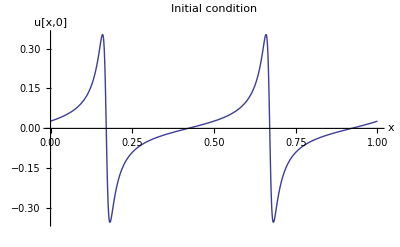

```mathematica
Plot[u[x,0],{x,0,1},PlotRange->Full, PlotLabel->"Initial condition",AxesLabel->{"x","u[x,0]"}]
```

```mathematica
Plot3D[u[x, t], {x, 0, 1}, {t, 0, 1}, PlotRange -> Full,PlotLabel->"Full solution",AxesLabel->{"x","t","u[x,t]"}]
```

-Graphics3D-

## The discrete approximation loaded from HDF5:

```mathematica
{uh,xh,th}=Map[
(Import[filename,{"Datasets",#} ])&,{"/u","/x","/t"}];
range =DataRange->{{Min[xh],Max[xh]},{Min[th],Max[th]}};
```

```mathematica
ListPlot3D[uh,range,PlotRange->Full,PlotLabel->"Discrete Approximation", AxesLabel->{"x","t","u^h[x,t]"}]
```

-Graphics3D-

## Error present in the discrete approximation:

```mathematica
exact = Table[u[ x,t],{t,th},{x,xh}];
error = exact - uh;
```

```mathematica
ListPlot3D[error,range,PlotRange->Full,PlotLabel->"Error evolution", AxesLabel->{"x","t","u-u^h"}]
```

-Graphics3D-

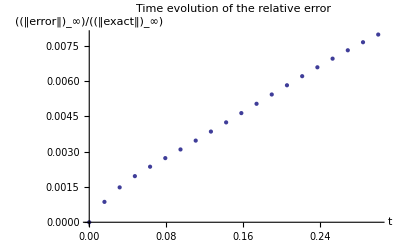

```mathematica
ListPlot[Apply[Norm[#,∞]&, error,{1}]/Apply[Norm[#,∞]&, exact,{1}],DataRange->{Min[th],Max[th]},PlotRange->Full,PlotLabel->"Time evolution of the relative error",AxesLabel->{"t","((‖error‖)_∞)/((‖exact‖)_∞)"} ]
```

## Investigating the exact and discrete solutions at each time step:

```mathematica
Manipulate[Show[
Plot[u[x,th[[i+1]]],{x,0,1}, PlotRange->Full],
ListPlot[uh[[i+1]],DataRange->{Min[xh],Max[xh]}],
PlotLabel->"Exact and Approximate Evolution",AxesLabel->{"x","u[x,t_i]"}
],
{{i,0,"Time step index"}, 0,Dimensions[error,1][[1]]-1,1}]
```